# Brownian Simulation

## Initialization

```mathematica
Q;
```

```mathematica
Q:=Quit[]
```

```mathematica
Off[General::obspkg]
<<VectorAnalysis`
```

```mathematica
Off[Solve::inex]
```

```mathematica
SetOptions[$FrontEndSession,"DefaultPrecision"->MachinePrecision,"DefaultRealPrecision"->MachinePrecision]
```

```mathematica
SetCoordinates[Cartesian[x,y,z]]
```

Cartesian[x,y,z]

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/bretton/Documents/School/Research/Optical-Binding-Simulation

```mathematica
$Assumptions={kg>0,second>0,meter>0,kelvin>0,coulomb>0,ϵb>0};
```

```mathematica
xx={1,0,0};
yy={0,1,0};
zz={0,0,1};
```

## Definitions

### Fundamental

```mathematica
ϵ0=8.85 10^-12 farad/meter
μ0=4π 10^-7 henry/meter
η0=√(μ0/ϵ0);
c=1/(√(ϵ0 μ0))//Simplify
kB=1.38 10^-23(kg meter^2)/(second^2 kelvin)
```

(8.85×10^-12 farad)/meter

(henry π)/(2500000 meter)

(2.99863×10^8 meter)/(√(farad henry))

(1.38×10^-23 kg meter^2)/(kelvin second^2)

### Colloid properties

```mathematica
a=500. 10^-9 meter
VOL=4/3 π a^3
ρSiO2=2320 kg/meter^3
mass=VOL ρSiO2
μ=1.6 10^-3 kg/(meter second) (*Dynamic Viscosity*)
γ=(6π μ a)/mass(*drag frequency*)
```

5.×10^-7 meter

5.23599×10^-19 meter^3

(2320 kg)/meter^3

1.21475×10^-15 kg

(0.0016 kg)/(meter second)

(1.24138×10^7)/second

```mathematica
T=300kelvin
```

300 kelvin

## Units

```mathematica
henry=henry/.Flatten[Solve[(farad henry)/meter^2==second^2/meter^2,henry]]
```

second^2/farad

```mathematica
(*kg=kg/.Flatten[Solve[newton==kg meter second^-2,kg]]*)
```

```mathematica
farad=coulomb/volt
volt=joule/coulomb
ampere=coulomb/second
joule=kg meter^2 second^-2
watt=joule/second
(*nm=meter 10^-9;
μm=meter 10^-6;*)
```

coulomb/volt

joule/coulomb

coulomb/second

(kg meter^2)/second^2

(kg meter^2)/second^3

```mathematica
second=10^6 microsecond
kg=10^9 microgram
meter=10^9 nanometer
coulomb=10^15 femtocoulomb
```

1000000 microsecond

1000000000 microgram

1000000000 nanometer

1000000000000000 femtocoulomb

```mathematica
microsecond=1
microgram=1
nanometer=1
femtocoulomb=1
```

1

1

1

«1 more identical outputs»

## Laser

```mathematica
λ=600.  10^-9 meter
area=100.(10^-6 meter)^2 
power=1000 watt
```

600.

1.×10^8

1000000000000

```mathematica
I0=power/area
```

10000.

```mathematica
I0
```

10000.

## Polarizability

```mathematica
ϵp=-3(1.33)^2(*SiO2*)
μp=1
ϵb=1.33^2(*SiO2*)
μb=1
ηb=√(μb/ϵb)
k0=(2π)/λ
ω=k0 c
k=k0 √ϵb
αsr=4π ϵ0 ϵb a^3(ϵp-ϵb)/(ϵp+2 ϵb)
αs=(1/αsr-ⅈ k^3/(6 π ϵ0 ϵb))^-1
```

-5.3067

1

1.7689

1

0.75188

0.010472

3.14016×10^9

0.0139277

98361.8

0.121279+109.221 ⅈ

```mathematica
k^3/(6 π ϵ0 ϵb)
```

0.00915573

```mathematica
1/αsr
```

0.0000101665

```mathematica
αr=ComplexExpand[Re[αsr]]//Simplify
αi=ComplexExpand[Im[αsr]]//Simplify
```

98361.8

0

## Physical Setup

```mathematica
L=25 10^-6 meter (*computational area*)
```

25000

```mathematica
NN=1(*Number of Particles*)
```

1

```mathematica
α=αr+ⅈ αi
```

98361.8

```mathematica
SeedRandom[1001010]
```

RandomGeneratorState[…]

```mathematica
RandomGeneratorState[…]
```

RandomGeneratorState[…]

```mathematica
polarizabilities=Table[{αx[m]=α,αy[m]=α,αz[m]=α},{m,1,NN}]
```

{{98361.8,98361.8,98361.8}}

```mathematica
(*Export["./test_files/starting_pol_arr.json", polarizabilities]*)
```

```mathematica
positions[0]=Table[{X[0][m]=RandomReal[{-L/2,L/2}],Y[0][m]=RandomReal[{-L/2,L/2}],Z[0][m]=RandomReal[{-L/2,L/2}]},{m,1,NN}]
```

{{-9888.3,-1688.19,10996.}}

```mathematica
(*Export["./test_files/starting_pos_arr.json", positions[0]]*)
```

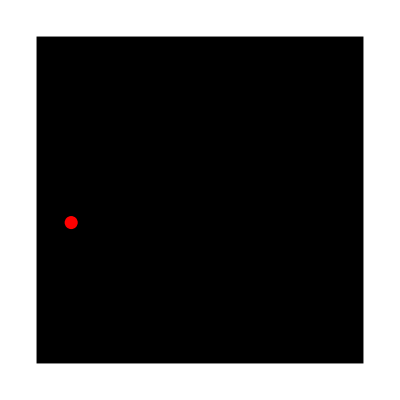

```mathematica
FRAME[0]=Graphics[{Rectangle[{-(L/2),-(L/2)},{L/2,L/2}],{Red,Table[Disk[{X[0][m],Y[0][m]},a],{m,1,NN}]}}]
```

## Green' s Function

```mathematica
k
```

0.0139277

```mathematica
ϵ0
```

8.85×10^-6

```mathematica
ϵb
```

1.7689

```mathematica
G[x_,y_,z_]={{(ⅇ^(ⅈ k √(x^2+y^2+z^2)) ((y^2+z^2) (-1+k^2 (y^2+z^2)+ⅈ k √(x^2+y^2+z^2))+x^2 (2+k^2 (y^2+z^2)-2 ⅈ k √(x^2+y^2+z^2))))/(4 π (x^2+y^2+z^2)^(5/2) ϵ0 ϵb),-(ⅇ^(ⅈ k √(x^2+y^2+z^2)) x y (-3+3 ⅈ k √(x^2+y^2+z^2)+k^2 (x^2+y^2+z^2)))/(4 π (x^2+y^2+z^2)^(5/2) ϵ0 ϵb),-(ⅇ^(ⅈ k √(x^2+y^2+z^2)) x z (-3+3 ⅈ k √(x^2+y^2+z^2)+k^2 (x^2+y^2+z^2)))/(4 π (x^2+y^2+z^2)^(5/2) ϵ0 ϵb)},{-(ⅇ^(ⅈ k √(x^2+y^2+z^2)) x y (-3+3 ⅈ k √(x^2+y^2+z^2)+k^2 (x^2+y^2+z^2)))/(4 π (x^2+y^2+z^2)^(5/2) ϵ0 ϵb),1/(4 π (x^2+y^2+z^2)^(5/2) ϵ0 ϵb)ⅇ^(ⅈ k √(x^2+y^2+z^2)) (k^2 x^4+z^2 (-1+k^2 z^2+ⅈ k √(x^2+y^2+z^2))+y^2 (2+k^2 z^2-2 ⅈ k √(x^2+y^2+z^2))+x^2 (-1+ⅈ k √(x^2+y^2+z^2)+k^2 (y^2+2 z^2))),-(ⅇ^(ⅈ k √(x^2+y^2+z^2)) y z (-3+3 ⅈ k √(x^2+y^2+z^2)+k^2 (x^2+y^2+z^2)))/(4 π (x^2+y^2+z^2)^(5/2) ϵ0 ϵb)},{-(ⅇ^(ⅈ k √(x^2+y^2+z^2)) x z (-3+3 ⅈ k √(x^2+y^2+z^2)+k^2 (x^2+y^2+z^2)))/(4 π (x^2+y^2+z^2)^(5/2) ϵ0 ϵb),-(ⅇ^(ⅈ k √(x^2+y^2+z^2)) y z (-3+3 ⅈ k √(x^2+y^2+z^2)+k^2 (x^2+y^2+z^2)))/(4 π (x^2+y^2+z^2)^(5/2) ϵ0 ϵb),1/(4 π (x^2+y^2+z^2)^(5/2) ϵ0 ϵb)ⅇ^(ⅈ k √(x^2+y^2+z^2)) (k^2 x^4+k^2 y^4+2 z^2 (1-ⅈ k √(x^2+y^2+z^2))+y^2 (-1+k^2 z^2+ⅈ k √(x^2+y^2+z^2))+x^2 (-1+ⅈ k √(x^2+y^2+z^2)+k^2 (2 y^2+z^2)))}}//Simplify;
```

```mathematica
GG[step_][n_][m_]=G[X[step][n]-X[step][m],Y[step][n]-Y[step][m],Z[step][n]-Z[step][m]];
GG[step_][n_][n_]=-{{1/αx[n],0,0},{0,1/αy[n],0},{0,0,1/αz[n]}};
```

```mathematica
GG[0][n_][m_]=G[X[0][n]-X[0][m],Y[0][n]-Y[0][m],Z[0][n]-Z[0][m]];
GG[0][n_][n_]=-{{1/αx[n],0,0},{0,1/αy[n],0},{0,0,1/αz[n]}};
```

```mathematica
GGtest = Table[GG[0][n][m], {n, 1, NN}, {m, 1, NN}];
```

```mathematica
(*Export["./test_files/G_mnij_real.json", Re[GGtest]]*)
```

```mathematica
(*Export["./test_files/G_mnij_imag.json", Im[GGtest]]*)
```

## Incident Field

```mathematica
w0=L/4
Einc[x_,y_,z_]=E0 xx Exp[ⅈ k z]Exp[-(x^2+y^2)/w0^2]
```

6250

{ⅇ^((-x^2-y^2)/39062500+(0.+0.0139277 ⅈ) z) E0,0,0}

```mathematica
EEi[step_][n_]=Einc[X[step][n],Y[step][n],Z[step][n]];
EEi[0][n_]=Einc[X[0][n],Y[0][n],Z[0][n]];
```

```mathematica
E0=√(2η0 ηb I0)
```

0.0752759

```mathematica
EEiTest = Table[EEi[0][n],{n,1,NN}];
```

```mathematica
(*Export["./test_files/Einc_mi_real.json",Re[EEiTest]]*)
```

```mathematica
(*Export["./test_files/Einc_mi_imag.json",Im[EEiTest]]*)
```

## Unknown Variables

```mathematica
pp[step_][m_]={px[step][m],py[step][m],pz[step][m]}
```

{px[step][m],py[step][m],pz[step][m]}

```mathematica
pp[0][m_]={px[0][m],py[0][m],pz[0][m]}
```

{px[0][m],py[0][m],pz[0][m]}

## Equations

```mathematica
eqX[step_][n_]:=(Sum[GG[step][n][m].pp[step][m],{m,1,NN}]+EEi[step][n]).xx
eqY[step_][n_]:=(Sum[GG[step][n][m].pp[step][m],{m,1,NN}]+EEi[step][n]).yy
eqZ[step_][n_]:=(Sum[GG[step][n][m].pp[step][m],{m,1,NN}]+EEi[step][n]).zz
```

```mathematica
eqs[step_]=Flatten[Table[{eqX[step][m]==0,eqY[step][m]==0,eqZ[step][m]==0},{m,1,NN}]]
```

{0.+0.0752759 ⅇ^((-(X[step][1])^2-(Y[step][1])^2)/39062500+(0.+0.0139277 ⅈ) Z[step][1])-0.0000101665 px[step][1]==0,0.-0.0000101665 py[step][1]==0,0.-0.0000101665 pz[step][1]==0}

```mathematica
unk[step_]=Flatten[Table[{px[step][m],py[step][m],pz[step][m]},{m,1,NN}]]
```

{px[step][1],py[step][1],pz[step][1]}

```mathematica
sol[0]=Solve[eqs[0],unk[0]]//Flatten
```

{px[0][1]→-396.893+399.658 ⅈ,py[0][1]→0.,pz[0][1]→0.}

```mathematica
Evaluate[unk[0]]=(unk[0]/.sol[0])
```

{-396.893+399.658 ⅈ,0.,0.}

```mathematica
(*Export["./test_files/p_i_real.json", Re[unk[0]]]*)
```

```mathematica
(*Export["./test_files/p_i_imag.json", Im[unk[0]]]*)
```

## Total Field

```mathematica
EEtot[step_][x_,y_,z_]=Einc[x,y,z]+Sum[G[x-X[step][m],y-Y[step][m],z-Z[step][m]].pp[step][m],{m,1,NN}];
```

```mathematica
II[step_][x_,y_,z_]=EEtot[step][x,y,z].(EEtot[step][x,y,z]/.ⅈ->-ⅈ);
```

```mathematica
(*DensityPlot[II[x,y,0],{x, -15λ,15λ},{y, -15λ,15λ},PlotPoints->50]*)
```

## Scattering at site m from all other particles

```mathematica
ESC[step_][m_][x_,y_,z_]:=Sum[G[x-X[step][i],y-Y[step][i],z-Z[step][i]].pp[step][i],{i,Drop[Table[j,{j,1,NN}],{m}]}]
```

```mathematica
ESCmi = Table[ESC[0][m][X[0][m],Y[0][m],Z[0][m]], {m, 1, NN}];
```

```mathematica
(*Export["./test_files/Esct_mi_real.json", Re[ESCmi]]*)
```

```mathematica
(*Export["./test_files/Esct_mi_imag.json",Im[ESCmi]]*)
```

```mathematica
Etot[step_][m_][x_,y_,z_]:=Einc[x,y,z]+ESC[step][m][x,y,z]
```

```mathematica
Htot[step_][m_][x_,y_,z_]:=Curl[Etot[step][m][x,y,z]]/(ⅈ ω μ0 μb)
```

```mathematica
ESC[0][1][x,y,z]
```

0

## Force on particle m

### Complex Force (must take real part)

```mathematica
cplxFF[step_][m_]:=((αr/4)Grad[Etot[step][m][x,y,z].(Etot[step][m][x,y,z]/.ⅈ->-ⅈ)]+αi (k/(ϵ0 ϵb))(1/2)(Cross[Etot[step][m][x,y,z],(Htot[step][m][x,y,z]/.ⅈ->-ⅈ)]/c)+αi (k/(ϵ0 ϵb))c Curl[(ϵ0 ϵb/(4 ω ⅈ))Cross[Etot[step][m][x,y,z],(Etot[step][m][x,y,z]/.ⅈ->-ⅈ)]])/.{x->X[step][m],y->Y[step][m],z->Z[step][m]}
```

```mathematica
cplxGradFF[step_][m_]:=((αr/4)Grad[Etot[step][m][x,y,z].(Etot[step][m][x,y,z]/.ⅈ->-ⅈ)])/.{x->X[step][m],y->Y[step][m],z->Z[step][m]}
cplxRadPFF[step_][m_]:=(αi (k/(ϵ0 ϵb))(1/2)(Cross[Etot[step][m][x,y,z],(Htot[step][m][x,y,z]/.ⅈ->-ⅈ)]/c))/.{x->X[step][m],y->Y[step][m],z->Z[step][m]}
cplxSpinFF[step_][m_]:=(αi (k/(ϵ0 ϵb))c Curl[(ϵ0 ϵb/(4 ω ⅈ))Cross[Etot[step][m][x,y,z],(Etot[step][m][x,y,z]/.ⅈ->-ⅈ)]])/.{x->X[step][m],y->Y[step][m],z->Z[step][m]}
```

### Force on all particles

```mathematica
Table[GradFF[0][m]=Re[cplxGradFF[0][m]],{m,1,NN}]
```

{{-5.66915×10^-6,-9.67869×10^-7,0.0224603}}

```mathematica
Table[RadPFF[0][m]=Re[cplxRadPFF[0][m]],{m,1,NN}]
```

{{0.,0.,0.}}

```mathematica
Table[SpinFF[0][m]=Re[cplxSpinFF[0][m]],{m,1,NN}]
```

{{0.,0.,0.}}

```mathematica
forces[0]=Table[FF[0][m]={Re[cplxFF[0][m]][[1]],Re[cplxFF[0][m]][[2]],0Re[cplxFF[0][m]][[3]]},{m,1,NN}]
```

{{-5.66915×10^-6,-9.67869×10^-7,0.}}

```mathematica
Etot[0][1]
```

Etot[0][1]

## Time Evolution

```mathematica
ϵ0
```

8.85×10^-6

```mathematica
8.849999999999998*^-6
k
```

8.85×10^-6

0.0139277

```mathematica
0.013927727430914747
```

0.0139277

```mathematica
ϵb
```

1.7689

```mathematica
velocities[0]=Table[{0,0,0},{i,1,NN}]
```

{{0,0,0}}

```mathematica
(*dt=tTH;*)
dt=10/γ;
(*dt=0.1;*)
Γ=(2γ kB T)/mass;
ΔB=Γ dt;
maxstep=500;
For[step=1,step≤maxstep,
positions[step]=positions[step-1]+velocities[step-1]dt;
Table[{X[step][m]=positions[step][[m]][[1]],Y[step][m]=positions[step][[m]][[2]],Z[step][m]=positions[step][[m]][[3]]},{m,1,NN}];
FRAME[step]=Graphics[{Rectangle[{-(L/2),-(L/2)},{L/2,L/2}],{Red,Table[Disk[{X[step][m],Y[step][m]},a],{m,1,NN}]}}];
randomΔV=Table[√ΔB({RandomVariate[NormalDistribution[]],RandomVariate[NormalDistribution[]],0}/(√2)),{i,1,NN}];
velocities[step]=velocities[step-1]Exp[-γ dt]+randomΔV+forces[step-1](dt/mass);
sol[step]=Solve[eqs[step],unk[step]]//Flatten;
Evaluate[unk[step]]=(unk[step]/.sol[step]);
forces[step]=Table[FF[step][m]={Re[cplxFF[step][m]][[1]],Re[cplxFF[step][m]][[2]],0Re[cplxFF[step][m]][[3]]},{m,1,NN}];
Print[step];
step++]
vel=Table[velocities[step][[1]],{step,0,maxstep,1}];
pos=Table[positions[step][[1]]-positions[0][[1]],{step,0,maxstep,1}];
(*ListPlot[vel,Joined->True]*)
(*ListPlot[pos,Joined->True]*)
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

201

202

203

204

205

206

207

208

209

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

241

242

243

244

245

246

247

248

249

250

251

252

253

254

255

256

257

258

259

260

261

262

263

264

265

266

267

268

269

270

271

272

273

274

275

276

277

278

279

280

281

282

283

284

285

286

287

288

289

290

291

292

293

294

295

296

297

298

299

300

301

302

303

304

305

306

307

308

309

310

311

312

313

314

315

316

317

318

319

320

321

322

323

324

325

326

327

328

329

330

331

332

333

334

335

336

337

338

339

340

341

342

343

344

345

346

347

348

349

350

351

352

353

354

355

356

357

358

359

360

361

362

363

364

365

366

367

368

369

370

371

372

373

374

375

376

377

378

379

380

381

382

383

384

385

386

387

388

389

390

391

392

393

394

395

396

397

398

399

400

401

402

403

404

405

406

407

408

409

410

411

412

413

414

415

416

417

418

419

420

421

422

423

424

425

426

427

428

429

430

431

432

433

434

435

436

437

438

439

440

441

442

443

444

445

446

447

448

449

450

451

452

453

454

455

456

457

458

459

460

461

462

463

464

465

466

467

468

469

470

471

472

473

474

475

476

477

478

479

480

481

482

483

484

485

486

487

488

489

490

491

492

493

494

495

496

497

498

499

500

```mathematica
Manipulate[Show[FRAME[step],PlotRange->{{-(L/2),L/2},{-(L/2),L/2}}],{step,1,maxstep,1}]
```

```mathematica
video=Table[Show[FRAME[step],PlotRange->{{-(L/2),L/2},{-(L/2),L/2}}],{step,1,maxstep}];
```

```mathematica
(*Export["video4.gif",video]*)
```

```mathematica
POSITIONS=Table[positions[step],{step,1,maxstep}]
```

{{{-9888.3,-1688.19,10996.}},{{-9895.55,-1694.62,10996.}},{{-9901.24,-1691.69,10996.}},{{-9906.6,-1687.58,10996.}},{{-9913.66,-1684.9,10996.}},{{-9916.46,-1686.,10996.}},{{-9913.56,-1691.51,10996.}},{{-9919.33,-1692.16,10996.}},{{-9928.6,-1686.91,10996.}},{{-9936.96,-1684.9,10996.}},{{-9940.56,-1684.69,10996.}},{{-9938.28,-1687.09,10996.}},{{-9948.6,-1685.78,10996.}},{{-9949.52,-1686.96,10996.}},{{-9949.03,-1685.15,10996.}},{{-9944.05,-1687.49,10996.}},{{-9944.83,-1686.36,10996.}},{{-9942.28,-1683.38,10996.}},{{-9948.34,-1678.72,10996.}},{{-9956.78,-1669.43,10996.}},{{-9958.69,-1671.28,10996.}},{{-9958.41,-1671.77,10996.}},{{-9964.12,-1675.27,10996.}},{{-9969.82,-1683.69,10996.}},{{-9970.39,-1686.81,10996.}},{{-9978.85,-1689.5,10996.}},{{-9984.84,-1697.53,10996.}},{{-9986.39,-1692.93,10996.}},{{-9992.93,-1692.57,10996.}},{{-9990.26,-1691.87,10996.}},{{-9997.57,-1689.89,10996.}},{{-10012.,-1683.92,10996.}},{{-10010.2,-1687.21,10996.}},{{-10003.7,-1684.31,10996.}},{{-9998.81,-1679.69,10996.}},{{-9992.32,-1677.49,10996.}},{{-9989.27,-1673.4,10996.}},{{-9985.62,-1674.33,10996.}},{{-9983.12,-1673.56,10996.}},{{-9986.26,-1671.65,10996.}},{{-9989.46,-1672.2,10996.}},{{-9990.8,-1678.28,10996.}},{{-9993.66,-1677.23,10996.}},{{-10000.4,-1682.9,10996.}},{{-10000.,-1679.62,10996.}},{{-9998.03,-1684.15,10996.}},{{-9991.32,-1684.27,10996.}},{{-9996.28,-1681.05,10996.}},{{-10005.6,-1685.34,10996.}},{{-10003.8,-1677.63,10996.}},{{-10003.2,-1688.58,10996.}},{{-9996.32,-1692.37,10996.}},{{-9996.41,-1690.22,10996.}},{{-9999.13,-1686.49,10996.}},{{-9998.33,-1693.39,10996.}},{{-10001.6,-1694.56,10996.}},{{-10002.7,-1692.58,10996.}},{{-10011.9,-1698.29,10996.}},{{-10017.1,-1704.44,10996.}},{{-10012.2,-1706.28,10996.}},{{-10005.2,-1706.12,10996.}},{{-10002.2,-1710.82,10996.}},{{-10003.8,-1705.28,10996.}},{{-10008.4,-1705.04,10996.}},{{-10009.7,-1698.01,10996.}},{{-10012.4,-1694.15,10996.}},{{-10026.1,-1695.95,10996.}},{{-10026.8,-1686.89,10996.}},{{-10029.,-1678.84,10996.}},{{-10031.9,-1674.14,10996.}},{{-10031.7,-1683.33,10996.}},{{-10029.6,-1685.45,10996.}},{{-10035.1,-1684.61,10996.}},{{-10031.7,-1690.37,10996.}},{{-10033.5,-1696.22,10996.}},{{-10039.2,-1692.86,10996.}},{{-10038.3,-1692.16,10996.}},{{-10047.,-1686.17,10996.}},{{-10043.,-1687.17,10996.}},{{-10039.3,-1686.81,10996.}},{{-10038.1,-1694.66,10996.}},{{-10044.9,-1695.29,10996.}},{{-10054.6,-1699.56,10996.}},{{-10058.,-1694.1,10996.}},{{-10059.8,-1699.85,10996.}},{{-10050.1,-1697.97,10996.}},{{-10050.,-1694.92,10996.}},{{-10048.1,-1694.3,10996.}},{{-10051.3,-1692.46,10996.}},{{-10061.9,-1693.74,10996.}},{{-10059.6,-1690.66,10996.}},{{-10056.4,-1689.75,10996.}},{{-10049.6,-1689.85,10996.}},{{-10059.7,-1693.14,10996.}},{{-10061.2,-1693.13,10996.}},{{-10065.1,-1699.11,10996.}},{{-10072.4,-1701.79,10996.}},{{-10069.4,-1696.7,10996.}},{{-10064.8,-1690.49,10996.}},{{-10065.9,-1691.61,10996.}},{{-10074.5,-1693.23,10996.}},{{-10076.6,-1690.09,10996.}},{{-10074.8,-1689.3,10996.}},{{-10078.3,-1694.28,10996.}},{{-10080.4,-1695.54,10996.}},{{-10082.3,-1696.73,10996.}},{{-10085.7,-1693.34,10996.}},{{-10088.5,-1688.34,10996.}},{{-10097.2,-1689.69,10996.}},{{-10100.3,-1685.5,10996.}},{{-10110.4,-1680.93,10996.}},{{-10114.6,-1689.35,10996.}},{{-10118.5,-1687.34,10996.}},{{-10120.,-1690.73,10996.}},{{-10129.5,-1690.69,10996.}},{{-10126.9,-1691.15,10996.}},{{-10127.,-1686.58,10996.}},{{-10124.1,-1682.09,10996.}},{{-10125.,-1687.36,10996.}},{{-10134.3,-1688.06,10996.}},{{-10144.4,-1687.95,10996.}},{{-10141.8,-1690.79,10996.}},{{-10142.1,-1695.11,10996.}},{{-10145.1,-1691.84,10996.}},{{-10152.3,-1698.2,10996.}},{{-10157.5,-1696.6,10996.}},{{-10155.1,-1699.63,10996.}},{{-10160.6,-1698.4,10996.}},{{-10158.5,-1700.47,10996.}},{{-10158.5,-1700.74,10996.}},{{-10170.4,-1700.13,10996.}},{{-10174.6,-1701.05,10996.}},{{-10179.,-1702.68,10996.}},{{-10184.3,-1698.24,10996.}},{{-10184.5,-1692.47,10996.}},{{-10185.7,-1690.29,10996.}},{{-10182.3,-1690.27,10996.}},{{-10192.2,-1693.14,10996.}},{{-10187.7,-1689.35,10996.}},{{-10190.8,-1697.37,10996.}},{{-10200.7,-1697.87,10996.}},{{-10205.3,-1703.01,10996.}},{{-10221.1,-1700.77,10996.}},{{-10218.8,-1707.14,10996.}},{{-10228.4,-1715.78,10996.}},{{-10233.6,-1722.22,10996.}},{{-10232.1,-1728.05,10996.}},{{-10235.1,-1731.9,10996.}},{{-10236.3,-1734.97,10996.}},{{-10234.6,-1737.89,10996.}},{{-10234.8,-1731.76,10996.}},{{-10240.3,-1731.2,10996.}},{{-10241.1,-1732.66,10996.}},{{-10250.8,-1728.54,10996.}},{{-10252.7,-1717.67,10996.}},{{-10256.5,-1721.85,10996.}},{{-10260.9,-1720.79,10996.}},{{-10267.9,-1716.48,10996.}},{{-10269.4,-1721.08,10996.}},{{-10272.2,-1717.01,10996.}},{{-10268.8,-1720.19,10996.}},{{-10278.3,-1724.89,10996.}},{{-10281.2,-1721.02,10996.}},{{-10281.7,-1720.4,10996.}},{{-10286.,-1724.51,10996.}},{{-10285.1,-1722.54,10996.}},{{-10286.3,-1717.99,10996.}},{{-10301.1,-1716.2,10996.}},{{-10305.8,-1716.12,10996.}},{{-10305.9,-1712.92,10996.}},{{-10305.5,-1712.06,10996.}},{{-10312.4,-1715.54,10996.}},{{-10316.6,-1721.55,10996.}},{{-10317.9,-1728.05,10996.}},{{-10323.5,-1729.29,10996.}},{{-10323.6,-1728.72,10996.}},{{-10325.8,-1730.24,10996.}},{{-10325.3,-1726.75,10996.}},{{-10322.7,-1724.74,10996.}},{{-10324.3,-1729.06,10996.}},{{-10329.3,-1721.17,10996.}},{{-10343.3,-1721.2,10996.}},{{-10356.9,-1725.92,10996.}},{{-10366.2,-1732.52,10996.}},{{-10365.9,-1731.37,10996.}},{{-10375.9,-1728.13,10996.}},{{-10382.9,-1725.54,10996.}},{{-10384.,-1735.04,10996.}},{{-10388.5,-1732.76,10996.}},{{-10394.1,-1738.2,10996.}},{{-10398.6,-1737.5,10996.}},{{-10403.6,-1734.9,10996.}},{{-10403.9,-1735.63,10996.}},{{-10401.5,-1747.17,10996.}},{{-10413.,-1748.09,10996.}},{{-10413.6,-1750.79,10996.}},{{-10412.5,-1751.54,10996.}},{{-10420.,-1753.14,10996.}},{{-10425.8,-1753.46,10996.}},{{-10434.,-1750.74,10996.}},{{-10430.9,-1749.6,10996.}},{{-10423.2,-1740.74,10996.}},{{-10430.1,-1738.09,10996.}},{{-10435.2,-1727.47,10996.}},{{-10442.7,-1720.55,10996.}},{{-10448.5,-1722.23,10996.}},{{-10447.,-1727.2,10996.}},{{-10454.1,-1720.99,10996.}},{{-10451.8,-1727.93,10996.}},{{-10447.9,-1740.31,10996.}},{{-10442.4,-1743.84,10996.}},{{-10445.8,-1735.13,10996.}},{{-10450.2,-1733.94,10996.}},{{-10455.8,-1735.91,10996.}},{{-10458.4,-1740.49,10996.}},{{-10461.6,-1740.46,10996.}},{{-10466.7,-1744.1,10996.}},{{-10475.8,-1745.51,10996.}},{{-10474.9,-1745.1,10996.}},{{-10473.6,-1751.58,10996.}},{{-10471.1,-1746.44,10996.}},{{-10477.6,-1747.83,10996.}},{{-10479.,-1745.08,10996.}},{{-10484.5,-1741.02,10996.}},{{-10485.6,-1742.07,10996.}},{{-10483.5,-1748.3,10996.}},{{-10478.2,-1752.14,10996.}},{{-10483.7,-1755.78,10996.}},{{-10482.7,-1750.94,10996.}},{{-10485.4,-1749.64,10996.}},{{-10489.9,-1752.43,10996.}},{{-10487.5,-1759.08,10996.}},{{-10489.3,-1761.57,10996.}},{{-10495.8,-1758.02,10996.}},{{-10494.8,-1761.12,10996.}},{{-10496.6,-1764.37,10996.}},{{-10494.1,-1766.43,10996.}},{{-10498.1,-1771.08,10996.}},{{-10502.8,-1767.48,10996.}},{{-10504.6,-1770.28,10996.}},{{-10505.9,-1765.71,10996.}},{{-10507.4,-1764.,10996.}},{{-10514.6,-1775.61,10996.}},{{-10510.9,-1771.45,10996.}},{{-10509.6,-1770.29,10996.}},{{-10512.6,-1771.63,10996.}},{{-10517.2,-1780.43,10996.}},{{-10515.9,-1781.6,10996.}},{{-10522.6,-1779.6,10996.}},{{-10526.4,-1782.87,10996.}},{{-10523.6,-1789.09,10996.}},{{-10529.,-1782.69,10996.}},{{-10537.,-1787.15,10996.}},{{-10532.5,-1782.54,10996.}},{{-10531.6,-1785.49,10996.}},{{-10530.,-1785.49,10996.}},{{-10537.5,-1785.66,10996.}},{{-10540.9,-1777.68,10996.}},{{-10550.5,-1783.95,10996.}},{{-10547.,-1777.59,10996.}},{{-10548.1,-1785.31,10996.}},{{-10547.9,-1781.97,10996.}},{{-10545.7,-1787.74,10996.}},{{-10540.,-1781.73,10996.}},{{-10543.1,-1790.79,10996.}},{{-10546.,-1783.66,10996.}},{{-10552.3,-1779.81,10996.}},{{-10565.6,-1787.07,10996.}},{{-10562.1,-1778.35,10996.}},{{-10565.1,-1776.89,10996.}},{{-10575.6,-1771.94,10996.}},{{-10577.4,-1775.26,10996.}},{{-10580.8,-1770.15,10996.}},{{-10574.9,-1763.38,10996.}},{{-10589.2,-1767.59,10996.}},{{-10592.1,-1768.17,10996.}},{{-10585.8,-1765.64,10996.}},{{-10585.6,-1768.74,10996.}},{{-10591.2,-1762.36,10996.}},{{-10586.6,-1763.6,10996.}},{{-10599.3,-1764.53,10996.}},{{-10591.5,-1772.01,10996.}},{{-10594.7,-1770.21,10996.}},{{-10595.5,-1768.44,10996.}},{{-10602.4,-1768.82,10996.}},{{-10609.5,-1772.23,10996.}},{{-10610.3,-1770.24,10996.}},{{-10615.8,-1769.35,10996.}},{{-10617.1,-1770.35,10996.}},{{-10621.2,-1768.61,10996.}},{{-10625.6,-1774.23,10996.}},{{-10621.1,-1765.58,10996.}},{{-10617.,-1768.53,10996.}},{{-10610.9,-1768.75,10996.}},{{-10609.,-1764.58,10996.}},{{-10613.7,-1769.1,10996.}},{{-10620.2,-1768.82,10996.}},{{-10613.7,-1765.34,10996.}},{{-10608.2,-1766.44,10996.}},{{-10614.1,-1770.17,10996.}},{{-10613.,-1776.95,10996.}},{{-10620.3,-1778.52,10996.}},{{-10624.4,-1786.9,10996.}},{{-10627.6,-1783.63,10996.}},{{-10633.9,-1785.2,10996.}},{{-10630.6,-1785.63,10996.}},{{-10631.9,-1785.16,10996.}},{{-10642.9,-1780.38,10996.}},{{-10639.2,-1782.97,10996.}},{{-10639.2,-1780.16,10996.}},{{-10644.7,-1775.51,10996.}},{{-10657.6,-1770.73,10996.}},{{-10665.3,-1776.58,10996.}},{{-10668.6,-1778.87,10996.}},{{-10663.7,-1776.49,10996.}},{{-10662.2,-1787.65,10996.}},{{-10664.5,-1797.44,10996.}},{{-10667.,-1801.45,10996.}},{{-10667.3,-1802.52,10996.}},{{-10671.,-1805.9,10996.}},{{-10669.6,-1806.9,10996.}},{{-10671.,-1809.48,10996.}},{{-10672.6,-1801.44,10996.}},{{-10673.,-1809.81,10996.}},{{-10674.3,-1810.3,10996.}},{{-10670.1,-1814.2,10996.}},{{-10671.8,-1814.1,10996.}},{{-10678.1,-1815.1,10996.}},{{-10679.6,-1811.23,10996.}},{{-10683.9,-1817.49,10996.}},{{-10694.4,-1824.47,10996.}},{{-10689.2,-1823.75,10996.}},{{-10684.4,-1823.45,10996.}},{{-10682.6,-1826.42,10996.}},{{-10684.1,-1818.35,10996.}},{{-10691.5,-1818.85,10996.}},{{-10702.6,-1813.58,10996.}},{{-10710.2,-1815.08,10996.}},{{-10713.5,-1821.24,10996.}},{{-10708.5,-1821.4,10996.}},{{-10708.1,-1818.07,10996.}},{{-10714.9,-1819.49,10996.}},{{-10720.,-1821.41,10996.}},{{-10718.1,-1824.72,10996.}},{{-10723.,-1838.12,10996.}},{{-10715.6,-1832.78,10996.}},{{-10726.1,-1833.12,10996.}},{{-10724.9,-1843.22,10996.}},{{-10725.7,-1845.56,10996.}},{{-10712.9,-1848.82,10996.}},{{-10704.8,-1841.74,10996.}},{{-10710.3,-1841.82,10996.}},{{-10711.8,-1844.11,10996.}},{{-10721.6,-1839.42,10996.}},{{-10727.8,-1836.45,10996.}},{{-10731.,-1838.54,10996.}},{{-10728.1,-1836.14,10996.}},{{-10742.3,-1834.63,10996.}},{{-10752.4,-1830.28,10996.}},{{-10754.8,-1826.18,10996.}},{{-10752.,-1824.27,10996.}},{{-10760.3,-1818.67,10996.}},{{-10763.8,-1814.19,10996.}},{{-10760.7,-1813.99,10996.}},{{-10755.6,-1811.15,10996.}},{{-10754.1,-1805.25,10996.}},{{-10753.4,-1805.17,10996.}},{{-10764.2,-1807.87,10996.}},{{-10769.,-1802.64,10996.}},{{-10774.6,-1803.68,10996.}},{{-10775.1,-1805.67,10996.}},{{-10772.2,-1802.26,10996.}},{{-10771.8,-1797.87,10996.}},{{-10774.1,-1798.62,10996.}},{{-10771.2,-1799.1,10996.}},{{-10768.8,-1794.6,10996.}},{{-10765.4,-1797.03,10996.}},{{-10767.3,-1794.9,10996.}},{{-10762.4,-1794.18,10996.}},{{-10765.5,-1806.47,10996.}},{{-10765.2,-1805.17,10996.}},{{-10772.3,-1810.28,10996.}},{{-10761.2,-1812.48,10996.}},{{-10767.3,-1813.53,10996.}},{{-10766.1,-1808.86,10996.}},{{-10768.,-1808.17,10996.}},{{-10780.4,-1805.07,10996.}},{{-10781.3,-1796.47,10996.}},{{-10792.,-1804.72,10996.}},{{-10791.7,-1812.19,10996.}},{{-10801.2,-1804.44,10996.}},{{-10809.2,-1812.22,10996.}},{{-10811.5,-1809.5,10996.}},{{-10815.9,-1810.09,10996.}},{{-10822.4,-1802.78,10996.}},{{-10814.9,-1798.99,10996.}},{{-10820.1,-1793.93,10996.}},{{-10822.,-1792.57,10996.}},{{-10827.6,-1785.25,10996.}},{{-10833.,-1788.52,10996.}},{{-10827.1,-1785.88,10996.}},{{-10826.7,-1792.54,10996.}},{{-10818.7,-1791.46,10996.}},{{-10819.6,-1791.7,10996.}},{{-10826.2,-1791.78,10996.}},{{-10827.7,-1796.66,10996.}},{{-10822.8,-1794.34,10996.}},{{-10819.2,-1792.22,10996.}},{{-10820.7,-1794.66,10996.}},{{-10820.9,-1799.41,10996.}},{{-10823.9,-1808.72,10996.}},{{-10820.9,-1806.49,10996.}},{{-10815.9,-1811.72,10996.}},{{-10815.2,-1814.48,10996.}},{{-10819.8,-1809.77,10996.}},{{-10811.4,-1809.55,10996.}},{{-10808.2,-1807.21,10996.}},{{-10809.6,-1810.42,10996.}},{{-10809.6,-1811.74,10996.}},{{-10805.6,-1819.29,10996.}},{{-10806.2,-1811.28,10996.}},{{-10810.5,-1807.97,10996.}},{{-10813.,-1801.87,10996.}},{{-10818.4,-1796.73,10996.}},{{-10822.3,-1796.2,10996.}},{{-10823.5,-1801.5,10996.}},{{-10830.5,-1801.9,10996.}},{{-10830.8,-1807.37,10996.}},{{-10826.3,-1815.09,10996.}},{{-10829.8,-1817.28,10996.}},{{-10822.1,-1816.74,10996.}},{{-10823.2,-1817.57,10996.}},{{-10815.2,-1813.81,10996.}},{{-10816.8,-1805.36,10996.}},{{-10818.9,-1802.03,10996.}},{{-10821.3,-1799.68,10996.}},{{-10830.5,-1797.54,10996.}},{{-10835.1,-1802.37,10996.}},{{-10834.1,-1799.01,10996.}},{{-10839.8,-1802.15,10996.}},{{-10833.4,-1803.36,10996.}},{{-10831.4,-1809.6,10996.}},{{-10837.6,-1807.22,10996.}},{{-10843.3,-1811.16,10996.}},{{-10841.8,-1814.06,10996.}},{{-10844.1,-1810.52,10996.}},{{-10840.7,-1812.73,10996.}},{{-10840.3,-1807.45,10996.}},{{-10837.5,-1811.95,10996.}},{{-10841.7,-1818.23,10996.}},{{-10842.4,-1821.91,10996.}},{{-10842.7,-1827.45,10996.}},{{-10839.9,-1836.11,10996.}},{{-10849.3,-1836.24,10996.}},{{-10855.3,-1836.65,10996.}},{{-10863.8,-1833.35,10996.}},{{-10851.4,-1836.03,10996.}},{{-10850.8,-1826.57,10996.}},{{-10849.5,-1831.85,10996.}},{{-10846.7,-1831.3,10996.}},{{-10853.1,-1828.34,10996.}},{{-10852.8,-1825.35,10996.}},{{-10851.8,-1827.16,10996.}},{{-10849.4,-1827.84,10996.}},{{-10843.9,-1827.76,10996.}},{{-10839.4,-1822.9,10996.}},{{-10844.2,-1822.93,10996.}},{{-10841.,-1824.92,10996.}},{{-10833.3,-1821.75,10996.}},{{-10836.8,-1829.48,10996.}},{{-10833.,-1827.76,10996.}},{{-10834.3,-1824.46,10996.}},{{-10827.8,-1822.67,10996.}},{{-10826.9,-1813.96,10996.}},{{-10837.8,-1809.94,10996.}},{{-10844.5,-1811.17,10996.}},{{-10845.2,-1810.45,10996.}},{{-10845.5,-1816.11,10996.}},{{-10851.5,-1818.55,10996.}},{{-10853.8,-1823.49,10996.}},{{-10850.7,-1826.17,10996.}},{{-10845.6,-1823.57,10996.}},{{-10850.8,-1829.87,10996.}},{{-10857.2,-1835.94,10996.}},{{-10860.6,-1823.89,10996.}},{{-10860.7,-1819.34,10996.}},{{-10858.3,-1806.09,10996.}},{{-10859.2,-1807.59,10996.}},{{-10856.9,-1805.62,10996.}},{{-10852.7,-1814.97,10996.}},{{-10851.5,-1812.02,10996.}},{{-10857.4,-1812.82,10996.}},{{-10860.2,-1822.6,10996.}},{{-10857.,-1835.59,10996.}},{{-10863.9,-1842.42,10996.}},{{-10869.1,-1848.72,10996.}},{{-10862.1,-1854.27,10996.}},{{-10868.5,-1857.17,10996.}},{{-10870.7,-1857.05,10996.}},{{-10872.1,-1860.76,10996.}}}

```mathematica
VELOCITIES=Table[velocities[step],{step,1,maxstep}];
```

```mathematica
DIPOLES=Table[unk[step],{step,1,maxstep}];
```

```mathematica
FORCES=Table[forces[step],{step,1,maxstep}]
```

{{{-5.66915×10^-6,-9.67869×10^-7,0.}},{{-5.62555×10^-6,-9.63378×10^-7,0.}},{{-5.59925×10^-6,-9.56667×10^-7,0.}},{{-5.57584×10^-6,-9.49838×10^-7,0.}},{{-5.54255×10^-6,-9.41998×10^-7,0.}},{{-5.52733×10^-6,-9.39756×10^-7,0.}},{{-5.53676×10^-6,-9.44715×10^-7,0.}},{{-5.50699×10^-6,-9.39451×10^-7,0.}},{{-5.46541×10^-6,-9.28598×10^-7,0.}},{{-5.42556×10^-6,-9.19952×10^-7,0.}},{{-5.40789×10^-6,-9.16511×10^-7,0.}},{{-5.41698×10^-6,-9.19568×10^-7,0.}},{{-5.3671×10^-6,-9.09449×10^-7,0.}},{{-5.36148×10^-6,-9.09052×10^-7,0.}},{{-5.36559×10^-6,-9.08814×10^-7,0.}},{{-5.38796×10^-6,-9.14331×10^-7,0.}},{{-5.38518×10^-6,-9.13172×10^-7,0.}},{{-5.40058×10^-6,-9.14401×10^-7,0.}},{{-5.37493×10^-6,-9.06985×10^-7,0.}},{{-5.34193×10^-6,-8.95668×10^-7,0.}},{{-5.33084×10^-6,-8.94628×10^-7,0.}},{{-5.33177×10^-6,-8.95075×10^-7,0.}},{{-5.3007×10^-6,-8.91206×10^-7,0.}},{{-5.26532×10^-6,-8.89198×10^-7,0.}},{{-5.25971×10^-6,-8.89845×10^-7,0.}},{{-5.21646×10^-6,-8.83187×10^-7,0.}},{{-5.18052×10^-6,-8.80742×10^-7,0.}},{{-5.17726×10^-6,-8.7767×10^-7,0.}},{{-5.14641×10^-6,-8.71681×10^-7,0.}},{{-5.15974×10^-6,-8.73812×10^-7,0.}},{{-5.12678×10^-6,-8.6658×10^-7,0.}},{{-5.06418×10^-6,-8.51746×10^-7,0.}},{{-5.06976×10^-6,-8.54506×10^-7,0.}},{{-5.10293×10^-6,-8.59178×10^-7,0.}},{{-5.12992×10^-6,-8.61771×10^-7,0.}},{{-5.16274×10^-6,-8.66709×10^-7,0.}},{{-5.1809×10^-6,-8.67904×10^-7,0.}},{{-5.19759×10^-6,-8.71499×10^-7,0.}},{{-5.21026×10^-6,-8.73444×10^-7,0.}},{{-5.19688×10^-6,-8.69929×10^-7,0.}},{{-5.18107×10^-6,-8.6729×10^-7,0.}},{{-5.1693×10^-6,-8.68351×10^-7,0.}},{{-5.15657×10^-6,-8.65423×10^-7,0.}},{{-5.1196×10^-6,-8.61544×10^-7,0.}},{{-5.12438×10^-6,-8.607×10^-7,0.}},{{-5.12968×10^-6,-8.64084×10^-7,0.}},{{-5.16145×10^-6,-8.70085×10^-7,0.}},{{-5.14076×10^-6,-8.6451×10^-7,0.}},{{-5.09276×10^-6,-8.5782×10^-7,0.}},{{-5.10833×10^-6,-8.56668×10^-7,0.}},{{-5.10121×10^-6,-8.611×10^-7,0.}},{{-5.13052×10^-6,-8.68594×10^-7,0.}},{{-5.132×10^-6,-8.67735×10^-7,0.}},{{-5.12243×10^-6,-8.63968×10^-7,0.}},{{-5.12008×10^-6,-8.67173×10^-7,0.}},{{-5.10359×10^-6,-8.64697×10^-7,0.}},{{-5.10001×10^-6,-8.6298×10^-7,0.}},{{-5.05197×10^-6,-8.56953×10^-7,0.}},{{-5.02239×10^-6,-8.54576×10^-7,0.}},{{-5.04353×10^-6,-8.5952×10^-7,0.}},{{-5.07623×10^-6,-8.6561×10^-7,0.}},{{-5.08645×10^-6,-8.7001×10^-7,0.}},{{-5.0837×10^-6,-8.66583×10^-7,0.}},{{-5.0622×10^-6,-8.62398×10^-7,0.}},{{-5.06269×10^-6,-8.5882×10^-7,0.}},{{-5.05345×10^-6,-8.55074×10^-7,0.}},{{-4.98793×10^-6,-8.43724×10^-7,0.}},{{-4.99255×10^-6,-8.39937×10^-7,0.}},{{-4.98919×10^-6,-8.3518×10^-7,0.}},{{-4.98006×10^-6,-8.31085×10^-7,0.}},{{-4.97286×10^-6,-8.34448×10^-7,0.}},{{-4.98102×10^-6,-8.3705×10^-7,0.}},{{-4.95643×10^-6,-8.32047×10^-7,0.}},{{-4.96707×10^-6,-8.36969×10^-7,0.}},{{-4.95351×10^-6,-8.37418×10^-7,0.}},{{-4.93019×10^-6,-8.3135×10^-7,0.}},{{-4.93502×10^-6,-8.31895×10^-7,0.}},{{-4.90032×10^-6,-8.22411×10^-7,0.}},{{-4.91803×10^-6,-8.26208×10^-7,0.}},{{-4.93495×10^-6,-8.29174×10^-7,0.}},{{-4.93368×10^-6,-8.32914×10^-7,0.}},{{-4.90247×10^-6,-8.27401×10^-7,0.}},{{-4.85478×10^-6,-8.20624×10^-7,0.}},{{-4.84391×10^-6,-8.15873×10^-7,0.}},{{-4.83107×10^-6,-8.16332×10^-7,0.}},{{-4.87621×10^-6,-8.23836×10^-7,0.}},{{-4.87954×10^-6,-8.2293×10^-7,0.}},{{-4.88864×10^-6,-8.2432×10^-7,0.}},{{-4.87571×10^-6,-8.20985×10^-7,0.}},{{-4.82667×10^-6,-8.12484×10^-7,0.}},{{-4.83973×10^-6,-8.13387×10^-7,0.}},{{-4.85495×10^-6,-8.15766×10^-7,0.}},{{-4.88548×10^-6,-8.21497×10^-7,0.}},{{-4.83695×10^-6,-8.14098×10^-7,0.}},{{-4.83012×10^-6,-8.12826×10^-7,0.}},{{-4.80802×10^-6,-8.11654×10^-7,0.}},{{-4.7731×10^-6,-8.06443×10^-7,0.}},{{-4.79056×10^-6,-8.07213×10^-7,0.}},{{-4.8162×10^-6,-8.08931×10^-7,0.}},{{-4.81046×10^-6,-8.08416×10^-7,0.}},{{-4.77097×10^-6,-8.01865×10^-7,0.}},{{-4.76408×10^-6,-7.99051×10^-7,0.}},{{-4.77269×10^-6,-8.00264×10^-7,0.}},{{-4.75285×10^-6,-7.99005×10^-7,0.}},{{-4.74251×10^-6,-7.97695×10^-7,0.}},{{-4.73311×10^-6,-7.96523×10^-7,0.}},{{-4.72098×10^-6,-7.92625×10^-7,0.}},{{-4.7128×10^-6,-7.88701×10^-7,0.}},{{-4.6737×10^-6,-7.82109×10^-7,0.}},{{-4.66344×10^-6,-7.78217×10^-7,0.}},{{-4.62321×10^-6,-7.68645×10^-7,0.}},{{-4.59817×10^-6,-7.6799×10^-7,0.}},{{-4.58324×10^-6,-7.64291×10^-7,0.}},{{-4.5739×10^-6,-7.6415×10^-7,0.}},{{-4.53355×10^-6,-7.56687×10^-7,0.}},{{-4.54416×10^-6,-7.58855×10^-7,0.}},{{-4.54749×10^-6,-7.57353×10^-7,0.}},{{-4.56347×10^-6,-7.58213×10^-7,0.}},{{-4.55545×10^-6,-7.59179×10^-7,0.}},{{-4.51532×10^-6,-7.52116×10^-7,0.}},{{-4.47252×10^-6,-7.44191×10^-7,0.}},{{-4.48119×10^-6,-7.47078×10^-7,0.}},{{-4.47678×10^-6,-7.48232×10^-7,0.}},{{-4.46651×10^-6,-7.44852×10^-7,0.}},{{-4.43162×10^-6,-7.41286×10^-7,0.}},{{-4.41137×10^-6,-7.36829×10^-7,0.}},{{-4.41885×10^-6,-7.3957×10^-7,0.}},{{-4.39717×10^-6,-7.35014×10^-7,0.}},{{-4.40402×10^-6,-7.37204×10^-7,0.}},{{-4.40384×10^-6,-7.37292×10^-7,0.}},{{-4.35516×10^-6,-7.28025×10^-7,0.}},{{-4.33733×10^-6,-7.25139×10^-7,0.}},{{-4.31792×10^-6,-7.22271×10^-7,0.}},{{-4.29981×10^-6,-7.16993×10^-7,0.}},{{-4.3034×10^-6,-7.15145×10^-7,0.}},{{-4.30024×10^-6,-7.13615×10^-7,0.}},{{-4.31403×10^-6,-7.16136×10^-7,0.}},{{-4.27173×10^-6,-7.09627×10^-7,0.}},{{-4.29261×10^-6,-7.1181×10^-7,0.}},{{-4.2743×10^-6,-7.11928×10^-7,0.}},{{-4.23389×10^-6,-7.04715×10^-7,0.}},{{-4.21193×10^-6,-7.02868×10^-7,0.}},{{-4.15063×10^-6,-6.90652×10^-7,0.}},{{-4.15546×10^-6,-6.94208×10^-7,0.}},{{-4.11122×10^-6,-6.89641×10^-7,0.}},{{-4.08662×10^-6,-6.87743×10^-7,0.}},{{-4.08789×10^-6,-6.90383×10^-7,0.}},{{-4.07354×10^-6,-6.89291×10^-7,0.}},{{-4.06675×10^-6,-6.8928×10^-7,0.}},{{-4.07143×10^-6,-6.91354×10^-7,0.}},{{-4.07488×10^-6,-6.89482×10^-7,0.}},{{-4.05403×10^-6,-6.85363×10^-7,0.}},{{-4.04981×10^-6,-6.85171×10^-7,0.}},{{-4.0156×10^-6,-6.77127×10^-7,0.}},{{-4.01605×10^-6,-6.72822×10^-7,0.}},{{-3.99872×10^-6,-6.71301×10^-7,0.}},{{-3.98267×10^-6,-6.67908×10^-7,0.}},{{-3.95931×10^-6,-6.61877×10^-7,0.}},{{-3.95043×10^-6,-6.62066×10^-7,0.}},{{-3.94243×10^-6,-6.58982×10^-7,0.}},{{-3.953×10^-6,-6.62188×10^-7,0.}},{{-3.91442×10^-6,-6.56916×10^-7,0.}},{{-3.90605×10^-6,-6.5385×10^-7,0.}},{{-3.90457×10^-6,-6.53335×10^-7,0.}},{{-3.88573×10^-6,-6.51466×10^-7,0.}},{{-3.89037×10^-6,-6.51553×10^-7,0.}},{{-3.88904×10^-6,-6.49534×10^-7,0.}},{{-3.83556×10^-6,-6.39017×10^-7,0.}},{{-3.81842×10^-6,-6.3584×10^-7,0.}},{{-3.82028×10^-6,-6.3496×10^-7,0.}},{{-3.82225×10^-6,-6.34991×10^-7,0.}},{{-3.79492×10^-6,-6.31312×10^-7,0.}},{{-3.77567×10^-6,-6.30056×10^-7,0.}},{{-3.7666×10^-6,-6.30833×10^-7,0.}},{{-3.74541×10^-6,-6.27395×10^-7,0.}},{{-3.74556×10^-6,-6.27208×10^-7,0.}},{{-3.73646×10^-6,-6.26098×10^-7,0.}},{{-3.74067×10^-6,-6.25571×10^-7,0.}},{{-3.75135×10^-6,-6.26782×10^-7,0.}},{{-3.74287×10^-6,-6.26839×10^-7,0.}},{{-3.73007×10^-6,-6.2154×10^-7,0.}},{{-3.67997×10^-6,-6.12371×10^-7,0.}},{{-3.62917×10^-6,-6.0478×10^-7,0.}},{{-3.59254×10^-6,-6.00427×10^-7,0.}},{{-3.59432×10^-6,-6.00343×10^-7,0.}},{{-3.56173×10^-6,-5.93213×10^-7,0.}},{{-3.53943×10^-6,-5.88218×10^-7,0.}},{{-3.52994×10^-6,-5.89814×10^-7,0.}},{{-3.51574×10^-6,-5.86408×10^-7,0.}},{{-3.49341×10^-6,-5.84201×10^-7,0.}},{{-3.47872×10^-6,-5.81259×10^-7,0.}},{{-3.46347×10^-6,-5.77566×10^-7,0.}},{{-3.46211×10^-6,-5.77568×10^-7,0.}},{{-3.46304×10^-6,-5.81697×10^-7,0.}},{{-3.4239×10^-6,-5.74788×10^-7,0.}},{{-3.42031×10^-6,-5.7504×10^-7,0.}},{{-3.4234×10^-6,-5.75865×10^-7,0.}},{{-3.39786×10^-6,-5.71684×10^-7,0.}},{{-3.37862×10^-6,-5.68235×10^-7,0.}},{{-3.3533×10^-6,-5.62656×10^-7,0.}},{{-3.36402×10^-6,-5.64255×10^-7,0.}},{{-3.3946×10^-6,-5.66917×10^-7,0.}},{{-3.37352×10^-6,-5.62166×10^-7,0.}},{{-3.36342×10^-6,-5.56792×10^-7,0.}},{{-3.34293×10^-6,-5.50784×10^-7,0.}},{{-3.32317×10^-6,-5.47761×10^-7,0.}},{{-3.32507×10^-6,-5.49733×10^-7,0.}},{{-3.30581×10^-6,-5.44215×10^-7,0.}},{{-3.30919×10^-6,-5.47088×10^-7,0.}},{{-3.31452×10^-6,-5.52101×10^-7,0.}},{{-3.33012×10^-6,-5.56116×10^-7,0.}},{{-3.32409×10^-6,-5.52155×10^-7,0.}},{{-3.31087×10^-6,-5.49353×10^-7,0.}},{{-3.29151×10^-6,-5.46468×10^-7,0.}},{{-3.28047×10^-6,-5.45935×10^-7,0.}},{{-3.27038×10^-6,-5.44083×10^-7,0.}},{{-3.25199×10^-6,-5.4189×10^-7,0.}},{{-3.22247×10^-6,-5.3694×10^-7,0.}},{{-3.22536×10^-6,-5.37339×10^-7,0.}},{{-3.22584×10^-6,-5.3948×10^-7,0.}},{{-3.23671×10^-6,-5.39839×10^-7,0.}},{{-3.21546×10^-6,-5.3639×10^-7,0.}},{{-3.21253×10^-6,-5.34986×10^-7,0.}},{{-3.19764×10^-6,-5.30989×10^-7,0.}},{{-3.19358×10^-6,-5.30576×10^-7,0.}},{{-3.19671×10^-6,-5.33106×10^-7,0.}},{{-3.21105×10^-6,-5.36944×10^-7,0.}},{{-3.19174×10^-6,-5.34545×10^-7,0.}},{{-3.19757×10^-6,-5.34095×10^-7,0.}},{{-3.19005×10^-6,-5.32308×10^-7,0.}},{{-3.17441×10^-6,-5.30314×10^-7,0.}},{{-3.17797×10^-6,-5.33045×10^-7,0.}},{{-3.17109×10^-6,-5.32554×10^-7,0.}},{{-3.15273×10^-6,-5.28071×10^-7,0.}},{{-3.15408×10^-6,-5.2928×10^-7,0.}},{{-3.1469×10^-6,-5.28964×10^-7,0.}},{{-3.15345×10^-6,-5.30812×10^-7,0.}},{{-3.13839×10^-6,-5.29462×10^-7,0.}},{{-3.12595×10^-6,-5.26055×10^-7,0.}},{{-3.11883×10^-6,-5.25597×10^-7,0.}},{{-3.11763×10^-6,-5.23978×10^-7,0.}},{{-3.11376×10^-6,-5.22742×10^-7,0.}},{{-3.08548×10^-6,-5.21047×10^-7,0.}},{{-3.09904×10^-6,-5.22296×10^-7,0.}},{{-3.10352×10^-6,-5.2277×10^-7,0.}},{{-3.09385×10^-6,-5.21391×10^-7,0.}},{{-3.075×10^-6,-5.20562×10^-7,0.}},{{-3.07827×10^-6,-5.2152×10^-7,0.}},{{-3.05899×10^-6,-5.1734×10^-7,0.}},{{-3.04593×10^-6,-5.15893×10^-7,0.}},{{-3.0508×10^-6,-5.18658×10^-7,0.}},{{-3.03818×10^-6,-5.144×10^-7,0.}},{{-3.01188×10^-6,-5.10835×10^-7,0.}},{{-3.02797×10^-6,-5.12462×10^-7,0.}},{{-3.02893×10^-6,-5.13515×10^-7,0.}},{{-3.03351×10^-6,-5.14368×10^-7,0.}},{{-3.01133×10^-6,-5.10292×10^-7,0.}},{{-3.00566×10^-6,-5.06894×10^-7,0.}},{{-2.97399×10^-6,-5.02865×10^-7,0.}},{{-2.98748×10^-6,-5.03509×10^-7,0.}},{{-2.98018×10^-6,-5.04407×10^-7,0.}},{{-2.98262×10^-6,-5.03887×10^-7,0.}},{{-2.98585×10^-6,-5.06169×10^-7,0.}},{{-3.00586×10^-6,-5.08123×10^-7,0.}},{{-2.99178×10^-6,-5.08165×10^-7,0.}},{{-2.98735×10^-6,-5.05257×10^-7,0.}},{{-2.97081×10^-6,-5.01071×10^-7,0.}},{{-2.92815×10^-6,-4.95268×10^-7,0.}},{{-2.94306×10^-6,-4.95528×10^-7,0.}},{{-2.93524×10^-6,-4.93666×10^-7,0.}},{{-2.9076×10^-6,-4.87169×10^-7,0.}},{{-2.90056×10^-6,-4.86817×10^-7,0.}},{{-2.89341×10^-6,-4.84062×10^-7,0.}},{{-2.91403×10^-6,-4.85919×10^-7,0.}},{{-2.87079×10^-6,-4.79202×10^-7,0.}},{{-2.86244×10^-6,-4.77837×10^-7,0.}},{{-2.88164×10^-6,-4.80639×10^-7,0.}},{{-2.88063×10^-6,-4.81324×10^-7,0.}},{{-2.86793×10^-6,-4.77218×10^-7,0.}},{{-2.88024×10^-6,-4.79811×10^-7,0.}},{{-2.84397×10^-6,-4.73456×10^-7,0.}},{{-2.86191×10^-6,-4.78809×10^-7,0.}},{{-2.85381×10^-6,-4.76828×10^-7,0.}},{{-2.85252×10^-6,-4.76098×10^-7,0.}},{{-2.83298×10^-6,-4.72632×10^-7,0.}},{{-2.81122×10^-6,-4.6959×10^-7,0.}},{{-2.81017×10^-6,-4.68853×10^-7,0.}},{{-2.79534×10^-6,-4.65904×10^-7,0.}},{{-2.7911×10^-6,-4.65401×10^-7,0.}},{{-2.78077×10^-6,-4.63047×10^-7,0.}},{{-2.76581×10^-6,-4.61829×10^-7,0.}},{{-2.78247×10^-6,-4.62539×10^-7,0.}},{{-2.79244×10^-6,-4.65153×10^-7,0.}},{{-2.80933×10^-6,-4.68294×10^-7,0.}},{{-2.81675×10^-6,-4.68509×10^-7,0.}},{{-2.80116×10^-6,-4.66898×10^-7,0.}},{{-2.78344×10^-6,-4.63591×10^-7,0.}},{{-2.80315×10^-6,-4.6624×10^-7,0.}},{{-2.81781×10^-6,-4.69211×10^-7,0.}},{{-2.79947×10^-6,-4.66881×10^-7,0.}},{{-2.79914×10^-6,-4.68664×10^-7,0.}},{{-2.77806×10^-6,-4.65224×10^-7,0.}},{{-2.76273×10^-6,-4.64661×10^-7,0.}},{{-2.75558×10^-6,-4.6247×10^-7,0.}},{{-2.73759×10^-6,-4.59583×10^-7,0.}},{{-2.74628×10^-6,-4.61295×10^-7,0.}},{{-2.74298×10^-6,-4.60563×10^-7,0.}},{{-2.7155×10^-6,-4.54259×10^-7,0.}},{{-2.72436×10^-6,-4.56564×10^-7,0.}},{{-2.7255×10^-6,-4.56029×10^-7,0.}},{{-2.71291×10^-6,-4.52505×10^-7,0.}},{{-2.68057×10^-6,-4.45368×10^-7,0.}},{{-2.65728×10^-6,-4.42638×10^-7,0.}},{{-2.6476×10^-6,-4.41458×10^-7,0.}},{{-2.6616×10^-6,-4.434×10^-7,0.}},{{-2.6603×10^-6,-4.46033×10^-7,0.}},{{-2.64947×10^-6,-4.46555×10^-7,0.}},{{-2.64067×10^-6,-4.45956×10^-7,0.}},{{-2.63954×10^-6,-4.46019×10^-7,0.}},{{-2.62806×10^-6,-4.44757×10^-7,0.}},{{-2.63137×10^-6,-4.45625×10^-7,0.}},{{-2.62641×10^-6,-4.4536×10^-7,0.}},{{-2.62604×10^-6,-4.4325×10^-7,0.}},{{-2.62085×10^-6,-4.44412×10^-7,0.}},{{-2.61718×10^-6,-4.43858×10^-7,0.}},{{-2.62637×10^-6,-4.46552×10^-7,0.}},{{-2.62188×10^-6,-4.45693×10^-7,0.}},{{-2.60506×10^-6,-4.42819×10^-7,0.}},{{-2.60298×10^-6,-4.41458×10^-7,0.}},{{-2.5889×10^-6,-4.40413×10^-7,0.}},{{-2.55838×10^-6,-4.3646×10^-7,0.}},{{-2.57225×10^-6,-4.38869×10^-7,0.}},{{-2.5846×10^-6,-4.41099×10^-7,0.}},{{-2.58788×10^-6,-4.42453×10^-7,0.}},{{-2.58787×10^-6,-4.40435×10^-7,0.}},{{-2.5685×10^-6,-4.36954×10^-7,0.}},{{-2.54273×10^-6,-4.30873×10^-7,0.}},{{-2.52267×10^-6,-4.27523×10^-7,0.}},{{-2.51139×10^-6,-4.26924×10^-7,0.}},{{-2.52387×10^-6,-4.29282×10^-7,0.}},{{-2.52666×10^-6,-4.2899×10^-7,0.}},{{-2.50869×10^-6,-4.25999×10^-7,0.}},{{-2.49509×10^-6,-4.23935×10^-7,0.}},{{-2.49833×10^-6,-4.25334×10^-7,0.}},{{-2.47962×10^-6,-4.25051×10^-7,0.}},{{-2.50071×10^-6,-4.27717×10^-7,0.}},{{-2.47429×10^-6,-4.22862×10^-7,0.}},{{-2.4727×10^-6,-4.24968×10^-7,0.}},{{-2.46955×10^-6,-4.24933×10^-7,0.}},{{-2.49989×10^-6,-4.31427×10^-7,0.}},{{-2.52376×10^-6,-4.34209×10^-7,0.}},{{-2.50979×10^-6,-4.31601×10^-7,0.}},{{-2.50494×10^-6,-4.31242×10^-7,0.}},{{-2.48265×10^-6,-4.2593×10^-7,0.}},{{-2.4686×10^-6,-4.2259×10^-7,0.}},{{-2.45972×10^-6,-4.21423×10^-7,0.}},{{-2.46795×10^-6,-4.22394×10^-7,0.}},{{-2.43372×10^-6,-4.15644×10^-7,0.}},{{-2.41094×10^-6,-4.10391×10^-7,0.}},{{-2.4071×10^-6,-4.0873×10^-7,0.}},{{-2.4146×10^-6,-4.0968×10^-7,0.}},{{-2.39704×10^-6,-4.0514×10^-7,0.}},{{-2.39064×10^-6,-4.02932×10^-7,0.}},{{-2.3982×10^-6,-4.04277×10^-7,0.}},{{-2.41169×10^-6,-4.06105×10^-7,0.}},{{-2.41818×10^-6,-4.05934×10^-7,0.}},{{-2.41983×10^-6,-4.06214×10^-7,0.}},{{-2.39241×10^-6,-4.01811×10^-7,0.}},{{-2.38313×10^-6,-3.98915×10^-7,0.}},{{-2.36915×10^-6,-3.96598×10^-7,0.}},{{-2.36711×10^-6,-3.96674×10^-7,0.}},{{-2.37559×10^-6,-3.97451×10^-7,0.}},{{-2.37841×10^-6,-3.96968×10^-7,0.}},{{-2.37279×10^-6,-3.96114×10^-7,0.}},{{-2.3795×10^-6,-3.97447×10^-7,0.}},{{-2.38725×10^-6,-3.97831×10^-7,0.}},{{-2.39424×10^-6,-3.9966×10^-7,0.}},{{-2.39057×10^-6,-3.98505×10^-7,0.}},{{-2.40293×10^-6,-4.00591×10^-7,0.}},{{-2.38988×10^-6,-4.01025×10^-7,0.}},{{-2.39124×10^-6,-4.00977×10^-7,0.}},{{-2.37193×10^-6,-3.98602×10^-7,0.}},{{-2.39754×10^-6,-4.0381×10^-7,0.}},{{-2.38234×10^-6,-4.01254×10^-7,0.}},{{-2.38729×10^-6,-4.01098×10^-7,0.}},{{-2.38312×10^-6,-4.00174×10^-7,0.}},{{-2.35471×10^-6,-3.94273×10^-7,0.}},{{-2.35648×10^-6,-3.92659×10^-7,0.}},{{-2.32742×10^-6,-3.89207×10^-7,0.}},{{-2.32505×10^-6,-3.90434×10^-7,0.}},{{-2.30594×10^-6,-3.85228×10^-7,0.}},{{-2.28407×10^-6,-3.82936×10^-7,0.}},{{-2.27997×10^-6,-3.81595×10^-7,0.}},{{-2.26949×10^-6,-3.79809×10^-7,0.}},{{-2.25755×10^-6,-3.76058×10^-7,0.}},{{-2.27646×10^-6,-3.78676×10^-7,0.}},{{-2.26656×10^-6,-3.75786×10^-7,0.}},{{-2.26287×10^-6,-3.74827×10^-7,0.}},{{-2.25298×10^-6,-3.71471×10^-7,0.}},{{-2.23935×10^-6,-3.69716×10^-7,0.}},{{-2.25392×10^-6,-3.71774×10^-7,0.}},{{-2.2521×10^-6,-3.72873×10^-7,0.}},{{-2.27075×10^-6,-3.7601×10^-7,0.}},{{-2.26874×10^-6,-3.75698×10^-7,0.}},{{-2.25357×10^-6,-3.72978×10^-7,0.}},{{-2.24809×10^-6,-3.73031×10^-7,0.}},{{-2.26028×10^-6,-3.74739×10^-7,0.}},{{-2.26933×10^-6,-3.75918×10^-7,0.}},{{-2.26497×10^-6,-3.75656×10^-7,0.}},{{-2.26252×10^-6,-3.76235×10^-7,0.}},{{-2.25182×10^-6,-3.76289×10^-7,0.}},{{-2.25962×10^-6,-3.77234×10^-7,0.}},{{-2.26885×10^-6,-3.80045×10^-7,0.}},{{-2.2692×10^-6,-3.80705×10^-7,0.}},{{-2.26056×10^-6,-3.7811×10^-7,0.}},{{-2.2802×10^-6,-3.81649×10^-7,0.}},{{-2.28863×10^-6,-3.82678×10^-7,0.}},{{-2.284×10^-6,-3.8253×10^-7,0.}},{{-2.28332×10^-6,-3.82693×10^-7,0.}},{{-2.28953×10^-6,-3.8548×10^-7,0.}},{{-2.29147×10^-6,-3.84084×10^-7,0.}},{{-2.28285×10^-6,-3.81789×10^-7,0.}},{{-2.27962×10^-6,-3.79875×10^-7,0.}},{{-2.26937×10^-6,-3.769×10^-7,0.}},{{-2.26068×10^-6,-3.75212×10^-7,0.}},{{-2.25562×10^-6,-3.75433×10^-7,0.}},{{-2.23942×10^-6,-3.72577×10^-7,0.}},{{-2.2365×10^-6,-3.7321×10^-7,0.}},{{-2.24353×10^-6,-3.76139×10^-7,0.}},{{-2.23476×10^-6,-3.75002×10^-7,0.}},{{-2.25246×10^-6,-3.78128×10^-7,0.}},{{-2.24969×10^-6,-3.77798×10^-7,0.}},{{-2.26955×10^-6,-3.80624×10^-7,0.}},{{-2.26937×10^-6,-3.78764×10^-7,0.}},{{-2.26601×10^-6,-3.77434×10^-7,0.}},{{-2.26134×10^-6,-3.76079×10^-7,0.}},{{-2.24138×10^-6,-3.72002×10^-7,0.}},{{-2.22884×10^-6,-3.70759×10^-7,0.}},{{-2.23249×10^-6,-3.70706×10^-7,0.}},{{-2.21837×10^-6,-3.68813×10^-7,0.}},{{-2.23221×10^-6,-3.7158×10^-7,0.}},{{-2.23417×10^-6,-3.73261×10^-7,0.}},{{-2.2211×10^-6,-3.70377×10^-7,0.}},{{-2.20672×10^-6,-3.68589×10^-7,0.}},{{-2.20896×10^-6,-3.69606×10^-7,0.}},{{-2.20528×10^-6,-3.68193×10^-7,0.}},{{-2.21201×10^-6,-3.69884×10^-7,0.}},{{-2.21504×10^-6,-3.69324×10^-7,0.}},{{-2.21942×10^-6,-3.71069×10^-7,0.}},{{-2.20732×10^-6,-3.70183×10^-7,0.}},{{-2.20433×10^-6,-3.70405×10^-7,0.}},{{-2.20141×10^-6,-3.71031×10^-7,0.}},{{-2.20407×10^-6,-3.73335×10^-7,0.}},{{-2.18295×10^-6,-3.69463×10^-7,0.}},{{-2.16959×10^-6,-3.67082×10^-7,0.}},{{-2.1522×10^-6,-3.63201×10^-7,0.}},{{-2.17835×10^-6,-3.68571×10^-7,0.}},{{-2.18374×10^-6,-3.676×10^-7,0.}},{{-2.18447×10^-6,-3.68831×10^-7,0.}},{{-2.19077×10^-6,-3.69876×10^-7,0.}},{{-2.17783×10^-6,-3.66882×10^-7,0.}},{{-2.17975×10^-6,-3.66616×10^-7,0.}},{{-2.18121×10^-6,-3.67259×10^-7,0.}},{{-2.18624×10^-6,-3.68324×10^-7,0.}},{{-2.1986×10^-6,-3.70578×10^-7,0.}},{{-2.21058×10^-6,-3.7176×10^-7,0.}},{{-2.19983×10^-6,-3.69796×10^-7,0.}},{{-2.20614×10^-6,-3.71369×10^-7,0.}},{{-2.22481×10^-6,-3.74127×10^-7,0.}},{{-2.21382×10^-6,-3.73738×10^-7,0.}},{{-2.22299×10^-6,-3.75067×10^-7,0.}},{{-2.22159×10^-6,-3.74109×10^-7,0.}},{{-2.23692×10^-6,-3.76546×10^-7,0.}},{{-2.24268×10^-6,-3.75742×10^-7,0.}},{{-2.21971×10^-6,-3.70698×10^-7,0.}},{{-2.20407×10^-6,-3.68108×10^-7,0.}},{{-2.2028×10^-6,-3.67726×10^-7,0.}},{{-2.19979×10^-6,-3.68362×10^-7,0.}},{{-2.1854×10^-6,-3.66241×10^-7,0.}},{{-2.17828×10^-6,-3.65963×10^-7,0.}},{{-2.18413×10^-6,-3.67591×10^-7,0.}},{{-2.1964×10^-6,-3.69299×10^-7,0.}},{{-2.1823×10^-6,-3.68022×10^-7,0.}},{{-2.16569×10^-6,-3.66215×10^-7,0.}},{{-2.16295×10^-6,-3.63237×10^-7,0.}},{{-2.1647×10^-6,-3.62622×10^-7,0.}},{{-2.17536×10^-6,-3.61835×10^-7,0.}},{{-2.17259×10^-6,-3.61641×10^-7,0.}},{{-2.1785×10^-6,-3.62307×10^-7,0.}},{{-2.18417×10^-6,-3.65274×10^-7,0.}},{{-2.18809×10^-6,-3.65375×10^-7,0.}},{{-2.17456×10^-6,-3.63079×10^-7,0.}},{{-2.1645×10^-6,-3.63255×10^-7,0.}},{{-2.16629×10^-6,-3.66256×10^-7,0.}},{{-2.14823×10^-6,-3.6432×10^-7,0.}},{{-2.1343×10^-6,-3.63021×10^-7,0.}},{{-2.1473×10^-6,-3.66564×10^-7,0.}},{{-2.13221×10^-6,-3.64345×10^-7,0.}},{{-2.12757×10^-6,-3.63456×10^-7,0.}},{{-2.12301×10^-6,-3.63353×10^-7,0.}}}

```mathematica
(*Export["positions4.csv",POSITIONS]*)
```

```mathematica
(*Export["velocities4.csv",VELOCITIES]*)
```

```mathematica
(*Export["dipoles4.csv",DIPOLES]*)
```

```mathematica
(*Export["forces4.csv",FORCES]*)
```

```mathematica
(x + y)*Conjugate[(x+y)]\\Expand
```

(x+y) Conjugate[x+y]

NSum::nslim: Limit of summation Drop[{1.,2.,3.},{m}] is not a number.

General::stop: Further output of NSum::nslim will be suppressed during this calculation.

$Aborted